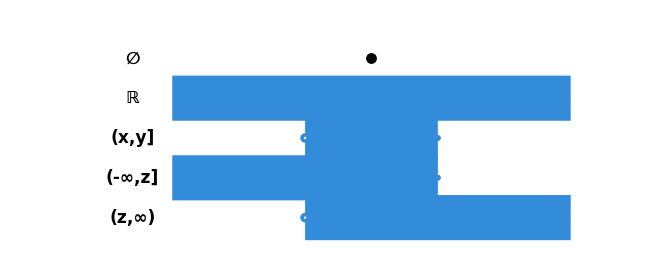

```mathematica
colorY = RGBColor[0.2, 0.55, 0.85];
sep = 0.6;
xMax = 3;

closedDot[c_] := {colorY, Disk[c, 0.045]};
openDot[c_] := {White, Disk[c, 0.045], colorY, Thickness[0.004], Circle[c, 0.045]};
segmento[x1_, x2_, y_] := {colorY, Thickness[0.05], CapForm["Round"], Line[{{x1, y}, {x2, y}}]};
rayoIzq[x_, y_] := {colorY, Thickness[0.05], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {-xMax, y}}]};
rayoDer[x_, y_] := {colorY, Thickness[0.05], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {xMax, y}}]};
rectaCompleta[y_] := {colorY, Thickness[0.05], CapForm["Round"],
   Arrowheads[{{0.03, 0}, {0.03, 1}}], Arrow[{{-xMax, y}, {xMax, y}}]};

y0 = 0; y1 = -sep; y2 = -2 sep; y3 = -3 sep; y4 = -4 sep;

filaVacio = {Black, PointSize[0.012], Point[{0, y0}]};
filaR = {rectaCompleta[y1]};
filaIntervalo = {segmento[-1, 1, y2], openDot[{-1, y2}], closedDot[{1, y2}]};
filaSemiIzq = {rayoIzq[1, y3], closedDot[{1, y3}]};
filaSemiDer = {rayoDer[-1, y4], openDot[{-1, y4}]};

etiquetas = {
   Text[Style["∅", 17, Bold], {-xMax - 0.6, y0}],
   Text[Style["ℝ", 17, Bold], {-xMax - 0.6, y1}],
   Text[Style["(x,y]", 17, Bold], {-xMax - 0.6, y2}],
   Text[Style["(-∞,z]", 17, Bold], {-xMax - 0.6, y3}],
   Text[Style["(z,∞)", 17, Bold], {-xMax - 0.6, y4}]
   };

grafico = Graphics[
   {filaVacio, filaR, filaIntervalo, filaSemiIzq, filaSemiDer, etiquetas},
   PlotRange -> {{-xMax - 1.7, xMax + 0.3}, {y4 - 0.5, y0 + 0.5}},
   ImageSize -> 650];

grafico
```

```mathematica
Export[CloudObject["T1_3_a.png"],grafico, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_a.png]

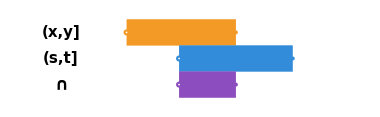
Intersección de dos intervalos
-Graphics-

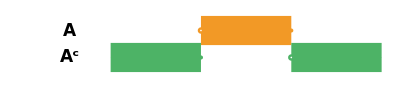
Complementario como unión disjunta
-Graphics-

```mathematica
colorA = RGBColor[0.95, 0.6, 0.15];
colorB = RGBColor[0.2, 0.55, 0.85];
colorInter = RGBColor[0.55, 0.3, 0.75];
colorComp = RGBColor[0.3, 0.7, 0.4];

sep = 0.6;
xMax = 3;

closedDot[c_, col_] := {col, Disk[c, 0.045]};
openDot[c_, col_] := {White, Disk[c, 0.045], col, Thickness[0.004], Circle[c, 0.045]};
segmento[x1_, x2_, y_, col_] := {col, Thickness[0.05], CapForm["Round"], Line[{{x1, y}, {x2, y}}]};
rayoIzq[x_, y_, col_] := {col, Thickness[0.05], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {-xMax, y}}]};
rayoDer[x_, y_, col_] := {col, Thickness[0.05], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {xMax, y}}]};

(* ---------- Panel A: cierre por intersección ---------- *)
yA1 = 0; yA2 = -sep; yA3 = -2 sep;

filaA = {segmento[-2, 0.5, yA1, colorA], openDot[{-2, yA1}, colorA], closedDot[{0.5, yA1}, colorA]};
filaB = {segmento[-0.8, 1.8, yA2, colorB], openDot[{-0.8, yA2}, colorB], closedDot[{1.8, yA2}, colorB]};
filaInter = {segmento[-0.8, 0.5, yA3, colorInter], openDot[{-0.8, yA3}, colorInter],
   closedDot[{0.5, yA3}, colorInter]};

etiquetasA = {
   Text[Style["(x,y]", 15, Bold], {-xMax - 0.5, yA1}],
   Text[Style["(s,t]", 15, Bold], {-xMax - 0.5, yA2}],
   Text[Style["∩", 17, Bold], {-xMax - 0.5, yA3}]
   };

panelA = Graphics[{filaA, filaB, filaInter, etiquetasA},
   PlotRange -> {{-xMax - 1.1, xMax}, {yA3 - 0.5, yA1 + 0.5}}, ImageSize -> 380];

tituloA = Style["Intersección de dos intervalos", 16, Bold];

(* ---------- Panel B: complementario como unión disjunta ---------- *)
yB1 = 0; yB2 = -sep;

filaOriginal = {segmento[-1, 1, yB1, colorA], openDot[{-1, yB1}, colorA], closedDot[{1, yB1}, colorA]};
filaComplemento = {
   rayoIzq[-1, yB2, colorComp], closedDot[{-1, yB2}, colorComp],
   rayoDer[1, yB2, colorComp], openDot[{1, yB2}, colorComp]
   };

etiquetasB = {
   Text[Style["A", 17, Bold], {-xMax - 0.9, yB1}],
   Text[Style["Aᶜ", 17, Bold], {-xMax - 0.9, yB2}]
   };

panelB = Graphics[{filaOriginal, filaComplemento, etiquetasB},
   PlotRange -> {{-xMax - 1.6, xMax}, {yB2 - 0.5, yB1 + 0.5}}, ImageSize -> 420];

tituloB = Style["Complementario como unión disjunta", 16, Bold];

diagramab=Column[{tituloA, panelA}, Alignment -> Center, Spacings -> 0.5]
diagramac= Column[{tituloB, panelB}, Alignment -> Center, Spacings -> 0.5]
```

```mathematica
Export[CloudObject["T1_3_b.png"],diagramab , "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
Export[CloudObject["T1_3_c.png"],diagramac , "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_b.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_c.png]

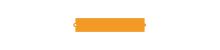
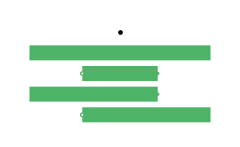
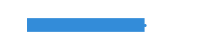
𝒢
-Graphics--Graphics-𝒴
-Graphics--Graphics-𝒞
-Graphics-

```mathematica
colorG = RGBColor[0.95, 0.6, 0.15];
colorC = RGBColor[0.2, 0.55, 0.85];
colorY = RGBColor[0.3, 0.7, 0.4];

closedDot[c_, col_] := {col, Disk[c, 0.045]};
openDot[c_, col_] := {White, Disk[c, 0.045], col, Thickness[0.004], Circle[c, 0.045]};
segmento[x1_, x2_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Line[{{x1, y}, {x2, y}}]};
rayoIzq[x_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {-2.4, y}}]};
rayoDer[x_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {2.4, y}}]};
rectaCompleta[y_, col_] := {col, Thickness[0.045], CapForm["Round"],
   Arrowheads[{{0.03, 0}, {0.03, 1}}], Arrow[{{-2.4, y}, {2.4, y}}]};

panelG = Graphics[
   {segmento[-1, 1, 0, colorG], openDot[{-1, 0}, colorG], closedDot[{1, 0}, colorG]},
   PlotRange -> {{-2.6, 2.6}, {-0.6, 0.6}}, ImageSize -> 220];

panelC = Graphics[
   {rayoIzq[1, 0, colorC], closedDot[{1, 0}, colorC]},
   PlotRange -> {{-2.6, 2.6}, {-0.6, 0.6}}, ImageSize -> 220];

sep = 0.55;
panelY = Graphics[
   {
    Black, PointSize[0.014], Point[{0, 2 sep}],
    rectaCompleta[1 sep, colorY],
    segmento[-1, 1, 0, colorY], openDot[{-1, 0}, colorY], closedDot[{1, 0}, colorY],
    rayoIzq[1, -1 sep, colorY], closedDot[{1, -1 sep}, colorY],
    rayoDer[-1, -2 sep, colorY], openDot[{-1, -2 sep}, colorY]
    },
   PlotRange -> {{-2.6, 2.6}, {-2 sep - 0.5, 2 sep + 0.5}}, ImageSize -> 240];

flechaDer[col_] := Graphics[{col, Thickness[0.008], Arrowheads[0.15], Arrow[{{0, 0}, {1, 0}}]},
   ImageSize -> {55, 35}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];
flechaIzq[col_] := Graphics[{col, Thickness[0.008], Arrowheads[0.15], Arrow[{{1, 0}, {0, 0}}]},
   ImageSize -> {55, 35}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];

columnaG = Column[{Style["𝒢", 22, Bold, colorG], panelG}, Alignment -> Center, Spacings -> 0.5];
columnaC = Column[{Style["𝒞", 22, Bold, colorC], panelC}, Alignment -> Center, Spacings -> 0.5];
columnaY = Column[{Style["𝒴", 22, Bold, colorY], panelY}, Alignment -> Center, Spacings -> 0.5];

diagramad = Row[{columnaG, flechaDer[colorG], columnaY, flechaIzq[colorC], columnaC}];

diagramad
```

```mathematica
Export[CloudObject["T1_3_d.png"],diagramad, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_d.png]

```mathematica
colorG = RGBColor[0.95, 0.6, 0.15];
colorC = RGBColor[0.2, 0.55, 0.85];
colorY = RGBColor[0.3, 0.7, 0.4];

icono[tipo_, col_] := Module[{contenido},
   contenido = Switch[tipo,
     "vacio", {Black, PointSize[0.05], Point[{0, 0}]},
     "recta", {col, Thickness[0.12], CapForm["Round"],
       Arrowheads[{{0.09, 0}, {0.09, 1}}], Arrow[{{-1, 0}, {1, 0}}]},
     "intervalo", {col, Thickness[0.12], CapForm["Round"], Line[{{-0.7, 0}, {0.7, 0}}],
       White, Disk[{-0.7, 0}, 0.1], col, Thickness[0.015], Circle[{-0.7, 0}, 0.1],
       Disk[{0.7, 0}, 0.1]},
     "semiIzq", {col, Thickness[0.12], CapForm["Round"], Arrowheads[0.09],
       Arrow[{{0.5, 0}, {-1, 0}}], Disk[{0.5, 0}, 0.1]},
     "semiDer", {col, Thickness[0.12], CapForm["Round"], Arrowheads[0.09],
       Arrow[{{-0.5, 0}, {1, 0}}], White, Disk[{-0.5, 0}, 0.1], col, Thickness[0.015],
       Circle[{-0.5, 0}, 0.1]},
     "dosRayos", {col, Thickness[0.1], CapForm["Round"], Arrowheads[0.08],
       Arrow[{{-0.3, 0}, {-1, 0}}], Disk[{-0.3, 0}, 0.1],
       Arrow[{{0.3, 0}, {1, 0}}], White, Disk[{0.3, 0}, 0.1], col, Thickness[0.015],
       Circle[{0.3, 0}, 0.1]}
     ];
   Graphics[contenido, PlotRange -> {{-1.3, 1.3}, {-0.35, 0.35}}, ImageSize -> 85]
   ];

masSigno = Style["+", 24, Bold, Gray];
igualSigno = Style["=", 24, Bold, Gray];
etiquetaY = Style["𝒴", 24, Bold, colorY];

filaG = Row[{
   icono["intervalo", colorG], masSigno, icono["recta", colorG], masSigno,
   icono["vacio", colorG], masSigno, icono["dosRayos", colorG], igualSigno, etiquetaY
   }, Spacer[6]];

filaC = Row[{
   icono["semiIzq", colorC], masSigno, icono["recta", colorC], masSigno,
   icono["vacio", colorC], masSigno, icono["semiDer", colorC], masSigno,
   icono["intervalo", colorC], igualSigno, etiquetaY
   }, Spacer[6]];

etiquetaG = Style["Desde 𝒢:", 18, Bold, colorG];
etiquetaC = Style["Desde 𝒞:", 18, Bold, colorC];

diagramae= Row[{etiquetaG, Spacer[15], filaG}]
diagramaf= Row[{etiquetaC, Spacer[15], filaC}]
```

Desde 𝒢:-Graphics-+-Graphics-+-Graphics-+-Graphics-=𝒴

Desde 𝒞:-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-=𝒴

```mathematica
Export[CloudObject["T1_3_e.png"],diagramae , "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
Export[CloudObject["T1_3_f.png"],diagramaf, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_e.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_f.png]

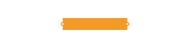
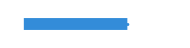
𝒜
-Graphics--Graphics-ℬ
-Graphics--Graphics-𝒞
-Graphics-

```mathematica
colorA = RGBColor[0.95, 0.6, 0.15];  (* 𝒜: abiertos *)
colorC = RGBColor[0.2, 0.55, 0.85];  (* 𝒞: semirrectas cerradas *)
colorB = RGBColor[0.3, 0.7, 0.4];    (* ℬ: Borel *)

closedDot[c_, col_] := {col, Disk[c, 0.045]};
openDot[c_, col_] := {White, Disk[c, 0.045], col, Thickness[0.004], Circle[c, 0.045]};
segmento[x1_, x2_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Line[{{x1, y}, {x2, y}}]};
rayoIzq[x_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {-2.2, y}}]};

blobPts[center_, r_, nPts_, seed_, varAmt_] := Module[{angles, radii},
   SeedRandom[seed];
   angles = Table[2 Pi k/nPts, {k, 0, nPts - 1}];
   radii = r (1 + varAmt RandomReal[{-1, 1}, nPts]);
   Table[center + radii[[k + 1]] {Cos[angles[[k + 1]]], Sin[angles[[k + 1]]]},
     {k, 0, nPts - 1}]
   ];
blobGraphic[pts_, col_, op_] := {col, Opacity[op],
   FilledCurve[{BSplineCurve[pts, SplineClosed -> True]}],
   Black, Opacity[1], Thickness[0.0035], BSplineCurve[pts, SplineClosed -> True]};

panelA = Graphics[{segmento[-1, 1, 0, colorA], openDot[{-1, 0}, colorA], openDot[{1, 0}, colorA]},
   PlotRange -> {{-2.4, 2.4}, {-0.6, 0.6}}, ImageSize -> 190];

panelC = Graphics[{rayoIzq[1, 0, colorC], closedDot[{1, 0}, colorC]},
   PlotRange -> {{-2.4, 2.4}, {-0.6, 0.6}}, ImageSize -> 190];

ptsB = blobPts[{0, 0}, 1.3, 14, 7, 0.12];
panelBorel = Graphics[{blobGraphic[ptsB, colorB, 0.5]},
   PlotRange -> {{-1.6, 1.6}, {-1.6, 1.6}}, ImageSize -> 210];

columnaA = Column[{Style["𝒜", 22, Bold, colorA], panelA}, Alignment -> Center, Spacings -> 0.5];
columnaC = Column[{Style["𝒞", 22, Bold, colorC], panelC}, Alignment -> Center, Spacings -> 0.5];
columnaB = Column[{Style["ℬ", 22, Bold, colorB], panelBorel}, Alignment -> Center, Spacings -> 0.5];

flechaDer[col_] := Graphics[{col, Thickness[0.008], Arrowheads[0.15], Arrow[{{0, 0}, {1, 0}}]},
   ImageSize -> {55, 35}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];
flechaIzq[col_] := Graphics[{col, Thickness[0.008], Arrowheads[0.15], Arrow[{{1, 0}, {0, 0}}]},
   ImageSize -> {55, 35}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];

diagramag = Row[{columnaA, flechaDer[colorA], columnaB, flechaIzq[colorC], columnaC}];

diagramag
```

```mathematica
Export[CloudObject["T1_3_g.png"],diagramag, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_g.png]

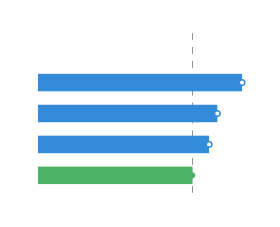
Semirrectas abiertas ∩ → semirrecta cerrada
-Graphics-

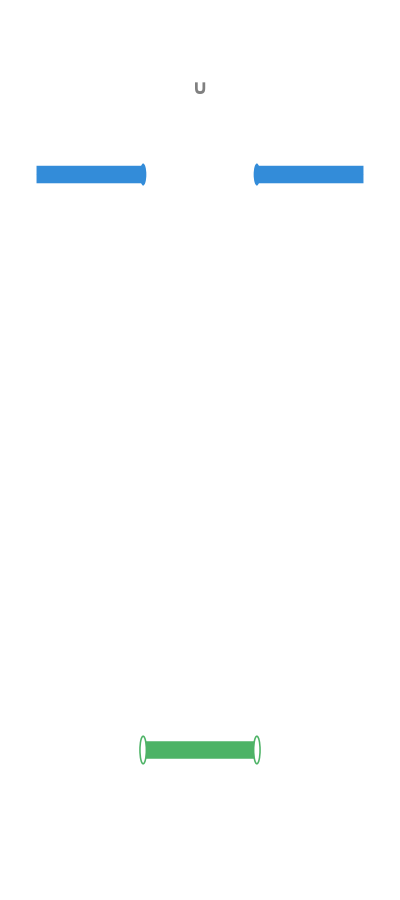
Dos semirrectas cerradas → (complemento) → intervalo abierto
-Graphics-

```mathematica
colorC = RGBColor[0.2, 0.55, 0.85];
colorMedio = RGBColor[0.55, 0.3, 0.75];
colorFinal = RGBColor[0.3, 0.7, 0.4];

closedDot[c_, col_] := {col, Disk[c, 0.045]};
openDot[c_, col_] := {White, Disk[c, 0.045], col, Thickness[0.004], Circle[c, 0.045]};
segmento[x1_, x2_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Line[{{x1, y}, {x2, y}}]};
rayoIzq[x_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {-2.3, y}}]};
rayoDer[x_, y_, col_] := {col, Thickness[0.045], CapForm["Round"], Arrowheads[0.03],
   Arrow[{{x, y}, {2.3, y}}]};

(* ---------- Panel 1: semirrectas abiertas encogiéndose hasta la cerrada ---------- *)
sepP = 0.5;
filasConv = Table[
   rayoIzq[0.2 + 0.8/n, -n sepP, colorC], {n, 1, 3}];
puntosConv = Table[openDot[{0.2 + 0.8/n, -n sepP}, colorC], {n, 1, 3}];
filaLimite = rayoIzq[0.2, -4 sepP, colorFinal];
puntoLimite = closedDot[{0.2, -4 sepP}, colorFinal];
guia = {Gray, Dashed, Thickness[0.0022], Line[{{0.2, 0.3}, {0.2, -4 sepP - 0.3}}]};

panel1Graf = Graphics[{guia, filasConv, puntosConv, filaLimite, puntoLimite},
   PlotRange -> {{-2.5, 1.2}, {-4 sepP - 0.5, 0.5}}, ImageSize -> 280];

signoInter = Style["∩", 22, Bold, Gray];

panel1 = Column[{panel1Graf}, Alignment -> Center];

(* ---------- Panel 2: dos semirrectas cerradas -> complemento -> intervalo abierto ---------- *)
filaRayo1 = {rayoIzq[-0.8, 0, colorC], closedDot[{-0.8, 0}, colorC]};
filaRayo2 = {rayoDer[0.8, 0, colorC], closedDot[{0.8, 0}, colorC]};
signoUnion = Text[Style["∪", 20, Bold, Gray], {0, 0.35}];

panelUnionGraf = Graphics[{filaRayo1, filaRayo2, signoUnion},
   PlotRange -> {{-2.3, 2.3}, {-0.4, 0.6}}, ImageSize -> 280];

flechaAbajo = Graphics[{Black, Thickness[0.007], Arrowheads[0.1], Arrow[{{0, 0.3}, {0, -0.3}}]},
   ImageSize -> {35, 55}, PlotRange -> {{-0.3, 0.3}, {-0.4, 0.4}}];

filaIntervalo = {segmento[-0.8, 0.8, 0, colorFinal], openDot[{-0.8, 0}, colorFinal],
   openDot[{0.8, 0}, colorFinal]};

panelIntervaloGraf = Graphics[filaIntervalo,
   PlotRange -> {{-2.3, 2.3}, {-0.4, 0.4}}, ImageSize -> 280];

panel2 = Column[{panelUnionGraf, flechaAbajo, panelIntervaloGraf}, Alignment -> Center, Spacings -> 0.3];

(* ---------- Composición final ---------- *)
titulo1 = Style["Semirrectas abiertas ∩ → semirrecta cerrada", 15, Bold];
titulo2 = Style["Dos semirrectas cerradas → (complemento) → intervalo abierto", 15, Bold];

diagramah=Column[{titulo1, panel1}, Alignment -> Center, Spacings -> 0.6]
diagramai=Column[{titulo2, panel2}, Alignment -> Center, Spacings -> 0.6]
```

```mathematica
Export[CloudObject["T1_3_h.png"],diagramah, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
Export[CloudObject["T1_3_i.png"],diagramai, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_h.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_i.png]

```mathematica
colorOmegaBg = LightGray;
colorE = RGBColor[0.75, 0.88, 1];
colorC = RGBColor[0.95, 0.6, 0.15];
colorTraza = RGBColor[0.2, 0.7, 0.4];

rE = 2.2;

grafico1 = Show[
   Graphics[{colorOmegaBg, EdgeForm[{Black, Thickness[0.003]}], Rectangle[{-5, -3}, {5, 3}]}],
   RegionPlot[x^2 + y^2 ≤ rE^2, {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorE, Opacity[0.6]], BoundaryStyle -> None, PlotPoints -> 80],

   (* tres conjuntos de ejemplo de la clase C *)
   RegionPlot[(x + 3.6)^2 + y^2 ≤ 1.0^2, {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorC, Opacity[0.5]], BoundaryStyle -> Directive[colorC, Thickness[0.003]],
     PlotPoints -> 60],
   RegionPlot[-1 ≤ x ≤ 1 && -3.0 ≤ y ≤ -0.6, {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorC, Opacity[0.5]], BoundaryStyle -> Directive[colorC, Thickness[0.003]],
     PlotPoints -> 60],
   RegionPlot[(x - 3.0)^2 + (y - 0.8)^2 ≤ 1.4^2, {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorC, Opacity[0.5]], BoundaryStyle -> Directive[colorC, Thickness[0.003]],
     PlotPoints -> 60],

   (* trazas: solo la parte de cada conjunto que cae dentro de E *)
   RegionPlot[x^2 + y^2 ≤ rE^2 && -1 ≤ x ≤ 1 && -3.0 ≤ y ≤ -0.6,
     {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorTraza, Opacity[0.9]], BoundaryStyle -> None, PlotPoints -> 80],
   RegionPlot[x^2 + y^2 ≤ rE^2 && (x - 3.0)^2 + (y - 0.8)^2 ≤ 1.4^2,
     {x, -5, 5}, {y, -3, 3},
     PlotStyle -> Directive[colorTraza, Opacity[0.9]], BoundaryStyle -> None, PlotPoints -> 80],

   Graphics[{
     FaceForm[None], EdgeForm[{Black, Thickness[0.004]}], Circle[{0, 0}, rE],
     Black,
     Text[Style["Ω", 22, Bold], {-4.4, 2.5}],
     Text[Style["E", 20, Bold], {0, 2.0}],
     Text[Style["𝒞", 17, Bold, colorC], {-3.6, 1.3}]
     }],
   PlotRange -> {{-5, 5}, {-3, 3}}, AspectRatio -> Automatic, ImageSize -> 620
   ];

diagramaj = Legended[grafico1,
   SwatchLegend[{colorC, colorTraza},
    {"conjuntos de 𝒞", "traza sobre E (𝒞∩E)"},
    LabelStyle -> Directive[FontSize -> 15], LegendMarkerSize -> 20]];

diagramaj
```

-Graphics-

```mathematica
Export[CloudObject["T1_3_j.png"],diagramaj, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_j.png]

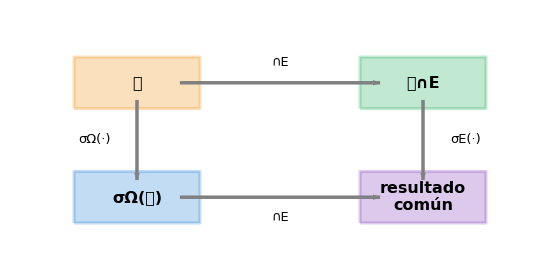

```mathematica
colorC = RGBColor[0.95, 0.6, 0.15];
colorCE = RGBColor[0.2, 0.7, 0.4];
colorSigmaOmega = RGBColor[0.2, 0.55, 0.85];
colorFinal = RGBColor[0.55, 0.3, 0.75];

nodo[pos_, label_, col_] := {
   col, Opacity[0.3], EdgeForm[{col, Thickness[0.004]}],
   Rectangle[pos - {1.1, 0.45}, pos + {1.1, 0.45}, RoundingRadius -> 0.15],
   Black, Opacity[1], Text[Style[label, 16, Bold], pos]
   };

flecha[from_, to_, etiqueta_, col_, despl_] := Module[{p1, p2, mid},
   p1 = from + 0.15 (to - from);
   p2 = from + 0.85 (to - from);
   mid = Mean[{p1, p2}];
   {col, Thickness[0.0045], Arrowheads[0.03], Arrow[{p1, p2}],
    Black, Text[Style[etiqueta, 13, Italic], mid + despl]}
   ];

topLeft = {0, 2}; topRight = {5, 2};
botLeft = {0, 0}; botRight = {5, 0};

diagramak = Graphics[{
    nodo[topLeft, "𝒞", colorC],
    nodo[topRight, "𝒞∩E", colorCE],
    nodo[botLeft, "σΩ(𝒞)", colorSigmaOmega],
    nodo[botRight, "resultado\ncomún", colorFinal],

    flecha[topLeft, topRight, "∩E", Gray, {0, 0.35}],
    flecha[topLeft, botLeft, "σΩ(·)", Gray, {-0.75, 0}],
    flecha[botLeft, botRight, "∩E", Gray, {0, -0.35}],
    flecha[topRight, botRight, "σE(·)", Gray, {0.75, 0}]
    },
   PlotRange -> {{-1.5, 6.5}, {-1, 3}}, ImageSize -> 560];
diagramak
```

```mathematica
Export[CloudObject["T1_3_k.png"],diagramak, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_3_k.png]